```mathematica
参数曲线
```

```mathematica
f[t_]:=Cos[t]
g[t_]:=Sin[t]
t1=0;t2=2Pi;

xi=f[t1+i(t2-t1)/n]
yi=g[t1+i(t2-t1)/n]
avg=Sum[Sqrt[(xi-x0)^2+(yi-y0)^2],{i,0,n}]/(n+1)
Limit[avg,n->Infinity]
```

Cos[(2 i π)/n]

Sin[(2 i π)/n]

(∑_(i=0)^n √((-x0+Cos[(2 i π)/n])^2+(-y0+Sin[(2 i π)/n])^2))/(1+n)

$Aborted

```mathematica
(Sum[Floor[j/s]-Floor[(j-1)/s],{s,1,j}]-2)/-j
```

-(-2+DivisorSigma[0,j])/j

```mathematica
sj=2/j-1/j∑_(s=1)^j (Floor[j/s]-Floor[(j-1)/s])
sj=2/j-1/j DivisorSigma[0,j]
pn=Floor[1+Sum[1-p[n,k],{k,1,2Floor[n Log[n]+1]}]]
pn=1+Sum[1-p[n,k],{k,1,2Floor[n Log[n]+1]}]
```

2/j-DivisorSigma[0,j]/j

1+∑_(k=1)^(2 (1+Floor[n Log[n]])) (1-p[n,k])

```mathematica
∑_(j=2)^k (1+Floor[2/j-1/j DivisorSigma[0,j]])
```

DivisorSigma[0,j]

```mathematica
$Line=816
```

816

```mathematica
∑_(j=2)^k (1+Floor[1/j(2-DivisorSigma[0,j])])/.k:>20
```

8

```mathematica
PrimePi[20]
```

8

```mathematica
t=1926;
1+∑_(k=1)^(4 (407+159 t)) (1-Floor[PrimePi[t]/(4 (407+159 t))])//TT
```

CPU Time:  3.42188

All Time:  3.42635

1226565

```mathematica
PrimePi[t]
```

```mathematica
9 (170+58 t+t^2)
```

34392186

```mathematica
1+∑_(k=1)^(9 (170+58 t+t^2)) (1-Floor[1/(4 (407+159 t))∑_(j=2)^k (1+Floor[2/j-1/j∑_(s=1)^j (Floor[j/s]-Floor[(j-1)/s])])])
```

2

```mathematica
$Line=816
```

816

```mathematica
∑_(s=1)^j (Floor[j/s]-Floor[(j-1)/s])
```

```mathematica
∑_(s=1)^(Sqrt@j) (Floor[(j-1)/s]-Floor[j/s])/.j->24
∑_(s=1)^j (Floor[j/s]-Floor[(j-1)/s])/.j->24
DivisorSigma[0,j]/.j->24
```

-4

8

```mathematica
2/j(1-DivisorSigma[0,j]/2)//FullSimplify
```

(2-DivisorSigma[0,j])/j

CPU Time:  1.60938

All Time:  1.60871

509

```mathematica
$Line=816
t=97;

t=150;
1+∑_(k=1)^(2Floor[t Log@t+1]) (1-Floor[1/t∑_(j=2)^k (1+Floor[1/j(2-DivisorSigma[0,j])])])//TT
Prime[t]
```

816

CPU Time:  1.76563

All Time:  1.75141

509

CPU Time:  5.34375

All Time:  5.34111

863

863

```mathematica
817//PrimePi
```

```mathematica
141//Prime
```

811

```mathematica
$Line=816
```

816

```mathematica
t=163;Prime[t]
1+∑_(k=1)^(2Floor[t Log@t+1]) (1-Floor[1/t∑_(j=2)^k (1+Floor[2/j(1+∑_(s=1)^(Sqrt@j) (Floor[(j-1)/s]-Floor[j/s]))])])//TT
1+∑_(k=1)^(2Floor[t Log@t+1]) (1-Floor[1/t∑_(j=2)^k (1+Floor[1/j(2-DivisorSigma[0,j])])])//TT
1+∑_(k=1)^(2Floor[t Log@t+1]) (1-Floor[1/t PrimePi[k]])//TT
```

967

CPU Time:  113.844

All Time:  114.452

967

CPU Time:  5.85938

All Time:  5.84999

967

CPU Time:  0.015625

All Time:  0.0114692

967

```mathematica
$Line=820
```

820

```mathematica
With[{t=1926},1+∑_(k=1)^(9t^2+522t+1530) (1-Floor[PrimePi[k]/(636t+1628)])//TT]
```

CPU Time:  278.5

All Time:  278.941

19260817

```mathematica
Quotient[1226564,1926]
Mod[1226564,1926]
Quotient[34392186,1926^2]
Mod[34392186,1926^2]
Quotient[1006902,1926]
Mod[1006902,1926]
```

```mathematica
CC
636t+1628//Factor
9t^2+522t+1530//Factor
```

所有临时定义已清空!

4 (407+159 t)

9 (170+58 t+t^2)

```mathematica
a+1+∑_(k=1)^a (1-f[k])
```

1+∑_(k=1)^a (1-f[k])

```mathematica
FieldHint
```

```mathematica
Expectation[Sqrt[x^2+(y-y0)^2],
{y\[Distributed]UniformDistribution[{c,d}]},
Assumptions->b>a&&d>c&&y>0]//TT
```

CPU Time:  66.5156

All Time:  80.6594

1/(2 (c-d))(c √(c^2+x^2-2 c y0+y0^2)-y0 √(c^2+x^2-2 c y0+y0^2)-d √(d^2+x^2-2 d y0+y0^2)+y0 √(d^2+x^2-2 d y0+y0^2)+x^2 Log[c-y0+√(c^2+x^2-2 c y0+y0^2)]-x^2 Log[d-y0+√(d^2+x^2-2 d y0+y0^2)])

```mathematica
AbsoluteTiming
```

```mathematica
MathematicalFunctionData
```

```mathematica
WolframLanguageData["RiemannSiegelTheta","EponymousPeople"]
```

{Bernhard Riemann,Carl Ludwig Siegel}

```mathematica
Entity["Person","BernhardRiemann::272q7"]
```

Bernhard Riemann

```mathematica
PersonData[Entity["Person","BernhardRiemann::272q7"],"NotableFacts"]
```

{Mathematician whose work in analysis and differential geometry influenced the development of the general theory of relativity,Theory of higher dimensions, leading to Riemannian geometry, is considered one of the key works in the field of geometry,Namesake of many theorems, equations, forms, functions, problems, and formulas}

```mathematica
PersonData[Entity["Person","BernhardRiemann::272q7"],"MathematicalAchievements"]
```

{Riemann hypothesis,Cauchy-Riemann equations,complete Riemannian metric,extended Riemann hypothesis,fundamental theorem of Riemannian geometry,generalized Riemann hypothesis,pseudo-Riemannian manifold,Riemann curve theorem,Riemann formula,Riemann function,Riemannian geometry,Riemannian manifold,Riemannian metric,Riemann integral,Riemann mapping theorem,Riemann method,Riemann prime counting function,Riemann P-differential equation,Riemann P-series,Riemann removable singularity theorem,Riemann series theorem,Riemann sphere,Riemann sphere place,Riemann sum,Riemann surface,Riemann tensor,Riemann theta function,Riemann zeta function,Riemann zeta function zeros,Riemann zeta function ζ(2),Riemann-Lebesgue lemma,Riemann-Liouville operator,Riemann-Siegel formula,Riemann-Siegel functions,Riemann-Siegel integral formula,Riemann-von Mangoldt formula,Riemann’s integral theorem,Riemann’s moduli problem,Riemann’s moduli space}

```mathematica
WolframLanguageData[All,"EponymousPeople"]//Flatten//Union//Length
```

299

```mathematica
2018-25+1
```

```mathematica
19940106
```

```mathematica
<<Deus`
```

```mathematica
Proof1926[19930106,114514]
```

1 + 9 + 9 + 3*0 - 10 - 6 == 1 - 1 + 4 - 5*1 + 4

```mathematica
1/Log[x]
```

1/Log[x]

```mathematica
∫1/Log[x] ⅆx
```

LogIntegral[x]

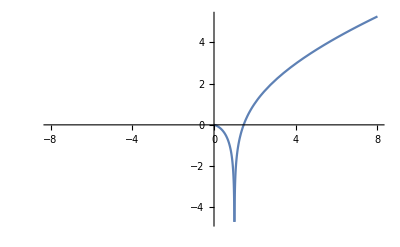

```mathematica
Plot[LogIntegral[x],{x,-8,8}]
```

```mathematica
D[R[x]E^g[x],x]//FullSimplify
```

ⅇ^g[x] (R[x] g'[x]+R'[x])

```mathematica
Integrate[E^E^x,x]
Integrate[E^x/x,x]
Integrate[1/Log@x,x]
```

ExpIntegralEi[ⅇ^x]

ExpIntegralEi[x]

LogIntegral[x]

```mathematica
LogIntegral[E^x]//FullSimplify
```

LogIntegral[ⅇ^x]

```mathematica
D[LogIntegral[ⅇ^x], x]
```

ⅇ^x/Log[ⅇ^x]

```mathematica
Integrate[1/Log@x,x]==LogIntegral[x]
```

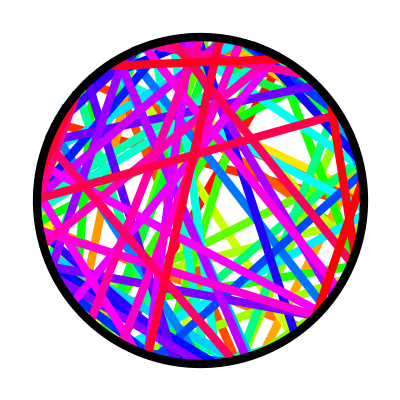

CPU Time:  5.

All Time:  14.2145

picking_1.gif

```mathematica
l=With[{n=100},Table[{Hue[i/n],Line[RandomPoint[Circle[],{2}]]},{i,n}]];
movie=Table[Graphics[{Thickness[.015],Take[l,n],Circle[{0,0},1]},AspectRatio->Automatic],{n,0,Length[l]}];
Show[Graphics[{Thickness[.015],l,Circle[{0,0},1]},AspectRatio->Automatic]]
Export["picking_1.gif",Show[#,PlotRange->Table[{-1,1},{2}]]&/@movie]//TT
```

```mathematica
Triangle/@RandomPoint[Circle[],{10^2,3}]
```

{Triangle[{{-0.123444,-0.992352},{0.78843,-0.615124},{0.669929,0.742426}}],98,Triangle[{{-0.639931,-0.768433},{-0.733849,-0.679312},{-0.985871,0.167506}}]}
 |  |  |  |

```mathematica
CC
```

所有临时定义已清空!

```mathematica
Area@Triangle[{{a,b},{c,d},{e,f}}]
```

1/2 Abs[Det[{{{0,#3-#4},-#2+#4},{{0,#5-#6},-#2+#6}}]]

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["picking_1.gif"]]]
```

CPU Time:  118.219

All Time:  138.721

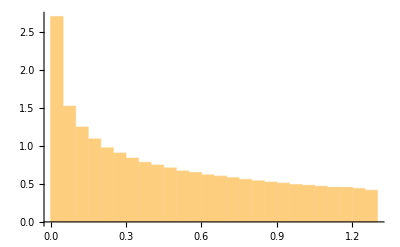

```mathematica
list=Triangle/@RandomPoint[Circle[],{10^6,3}];
data=ParallelMap[Area,list];//TT
Show[
(*Plot[Piecewise[{{2/(Pi*Sqrt[4 - x^2]), 0 < x < 2}}, 0],{x,0,2}],*)
Histogram[data,Automatic,"PDF"]
]
```

```mathematica
PDF[UniformDistribution[{0,3Sqrt[3]/4}],x]
```

Piecewise[{{4/(3 √3), 0≤x≤(3 √3)/4}, {0, True}}]

```mathematica
FindDistribution[data,5,PerformanceGoal->"Quality",TargetFunctions->"Continuous"]//TableForm//TT
```

CPU Time:  113.766

All Time:  117.827

MixtureDistribution[{0.4779,0.5221},{BetaDistribution[0.543876,1.36541],UniformDistribution[{2.64697×10^-9,1.29904}]}]
MixtureDistribution[{0.692005,0.307995},{BetaDistribution[0.700748,1.89487],GammaDistribution[22.2305,0.0428036]}]
MixtureDistribution[{0.457021,0.542979},{HalfNormalDistribution[3.72224],UniformDistribution[{2.64697×10^-9,1.29904}]}]
DataDistribution[…]
HalfNormalDistribution[1.96515]

```mathematica
FindDistributionParameters[data,MixtureDistribution[{a,b},{BetaDistribution[c,d],UniformDistribution[{0,3Sqrt[3]/4}]}]]
```

{a→0.39418,b→0.60582,c→0.597965,d→2.18414}

```mathematica
FindDistributionParameters[data,MixtureDistribution[{1,1},{BetaDistribution[c,d],UniformDistribution[{0,3Sqrt[3]/4}]}]]
```

{c→0.586146,d→1.57458}

```mathematica
Pi/2//N
```

1.5708

```mathematica
FindDistributionParameters[data[[1;;10^5]],MixtureDistribution[{1,1},{GammaDistribution[a,1,c,0],UniformDistribution[{0,3Sqrt[3]/4}]}]]
```

{a→0.115869,c→4.50808}

```mathematica
GammaDistribution[a,1,c,0]/.%
```

GammaDistribution[0.115869,1,4.50808,0]

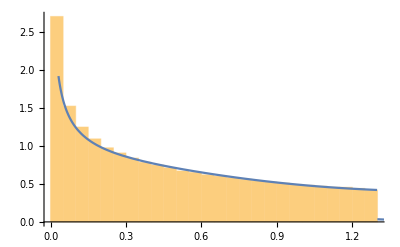

```mathematica
𝒟=TransformedDistribution[Piecewise[{
{2Sin[t1/2] Sin[t2/2] Sin[(t2-t1)/2 ],t1<t2<2 π},
{2Sin[t1/2]  Sin[t2/2]Sin[(t1-t2)/2],0<t2<t1}
},0],
{t1\[Distributed]UniformDistribution[{0, π}],
t2\[Distributed]UniformDistribution[{0, 2π}]}
];
ℳ=MixtureDistribution[{1,1},{GammaDistribution[1/5,1,5/2,0],
UniformDistribution[{0,(3 √3)/4}]}];
Show[Histogram[data,Automatic,"PDF"],Plot[PDF[ℳ,x],{x,0,2}]]
```

```mathematica
PDF[𝒟,x]//TT
```

$Aborted

```mathematica
.
```

```mathematica
FindInstance[Gamma[2/5+a]/Gamma[a]==3/π-(3 √3)/8,{a}]//N
```

{{a→0.184672}}

```mathematica
{Moment[ℳ,1]==Moment[𝒟,1],Moment[ℳ,2]==Moment[𝒟,2],Moment[ℳ,3]==Moment[𝒟,3]}
```

{1/2 ((3 √3)/8+Gamma[a+1/c]/Gamma[a])==3/(2 π),1/2 (9/16+Gamma[a+2/c]/Gamma[a])==3/8,1/2 ((81 √3)/256+Gamma[a+3/c]/Gamma[a])==35/(32 π)}

```mathematica
Solve[{1/2 ((3 √3)/8+Gamma[a+1/c]/Gamma[a])==3/(2 π),1/2 (9/16+Gamma[a+2/c]/Gamma[a])==3/8},{a,c}]
```

Solve[{1/2 ((3 √3)/8+Gamma[a+1/c]/Gamma[a])==3/(2 π),1/2 (9/16+Gamma[a+2/c]/Gamma[a])==3/8},{a,c}]

```mathematica
特殊函数
```

```mathematica
Alikoski[n_]:=Module[{ω=2Pi/n},
(9Cos[ω]^2+52Cos[ω]+44)/(36n^2Sin[ω]^2)
]
RegularPolygonArea[n_]:=1/4 n a^2 Cot[π/n]
```

```mathematica
Grid[RootReduce[Table[{n,area=Alikoski[n],N[area]},{n,3,10}]],Dividers->All,Alignment->{{Decimal,Center,Decimal},Automatic}]//TraditionalForm
```

3 | 1/12 | 0.0833333
4 | 11/144 | 0.0763889
5 | 1/180 (9+2 √5) | 0.0748452
6 | 289/3888 | 0.0743313
7 | Root[784147392 #1^3-84015792 #1^2+2125620 #1-15289&,3] | 0.0741193
8 | (97+52 √2)/2304 | 0.0740187
9 | Root[24794911296 #1^3-2525407632 #1^2+55366092 #1-312427&,3] | 0.073966
10 | (745+262 √5)/18000 | 0.0739361

```mathematica
Grid[Table[{n,area=Alikoski[n]RegularPolygonArea[n],N[area/a^2]},{n,3,10}]//FullSimplify,Dividers->All,Alignment->{{Decimal,Center,Decimal},Automatic}]//TraditionalForm
```

3 | a^2/(16 √3) | 0.0360844
4 | (11 a^2)/144 | 0.0763889
5 | 1/144 √(173+382/(√5)) a^2 | 0.128769
6 | (289 a^2)/(864 √3) | 0.193118
7 | (a^2 (44+sin((3 π)/14) (52+9 sin((3 π)/14))) cot(π/7) sec^2((3 π)/14))/1008 | 0.269343
8 | ((97+52 √2) a^2 cot(π/8))/1152 | 0.357394
9 | (a^2 (44+cos((2 π)/9) (52+9 cos((2 π)/9))) cot(π/9) csc^2((2 π)/9))/1296 | 0.457245
10 | (√(335801+749678/(√5)) a^2)/1440 | 0.56888

```mathematica
Integrate[Log@Log@x,{x,3,5}]//FullSimplify
```

-3 Log[Log[3]]+5 Log[Log[5]]+LogIntegral[3]-LogIntegral[5]

```mathematica
Total/@(Tuples[2 Range[50]-1,2]^2)//Tally//MaximalBy[Last]
```

{{8450,9}}